Abrams-Strogatz model Phase Space and Fixed Points

Setting the values of the model’s parameters

```mathematica
alpha=1.5;
s=0.3;
c=1;
```

Finding the fixed points of the system

```mathematica
Solve[0== (1-x)*c*s*x^alpha-x*(1-x)^(alpha)*c*(1-s), x]
```

{{x→0.},{x→0.844828},{x→1.}}

Plot dp_A/dt vs p_A

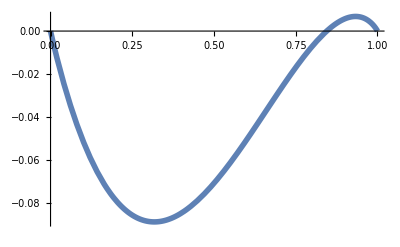

```mathematica
a=Plot[(1-x)*c*s*x^alpha-x*(1-x)^(alpha)*c*(1-s),{x, 0 ,1},PlotStyle-> Thickness[0.01]]
```

Plot in green the stable fixed points (determine which ones are stable which ones the unstables by looking at the above plot)

```mathematica
b=ListPlot[{{1,0},{0,0}}, PlotStyle->Green, PlotMarkers->{Automatic, AbsolutePointSize[50]}];
```

Plot in red the unstable fixed points

```mathematica
d=ListPlot[{{0.8448275862068966,0}}, PlotStyle-> Red, PlotMarkers->{Automatic, AbsolutePointSize[50]}];
```

Plot together dp_A/dt vs p_A and the fixed points together

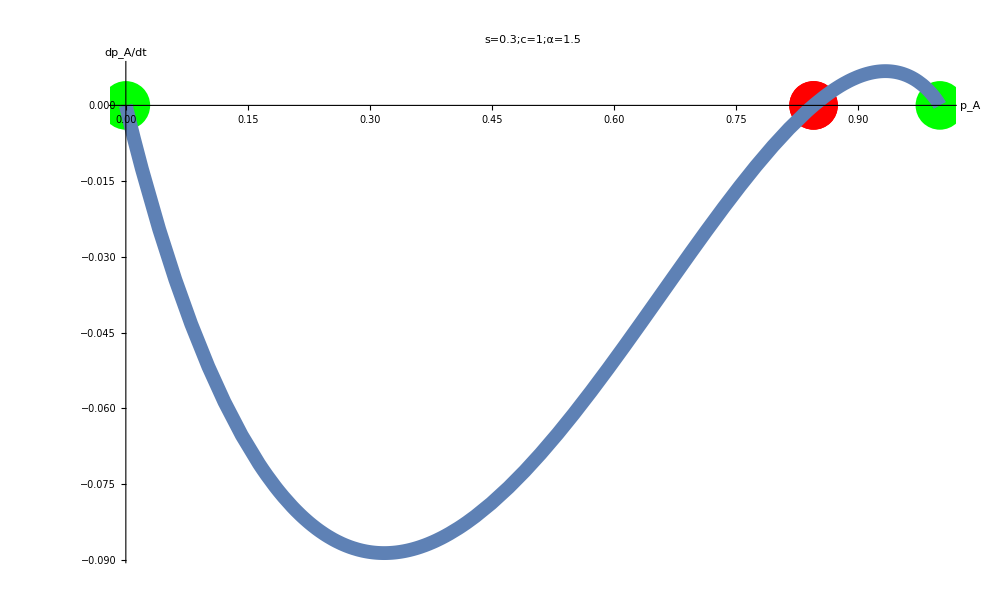

```mathematica
Show[b,d,a, AxesLabel->{HoldForm[Subscript[p, A]],HoldForm[Subscript[dp, A]/dt]},PlotLabel->HoldForm[s=0.3;  c=1;      α=1.5],LabelStyle->{50,GrayLevel[0]}, PlotRange->All, PlotLegends-> {HoldForm[s=0.3], HoldForm[s=0.7]}]
```